## Section | Wolfram Language Basics

### Getting Started

If you have no experience with the Wolfram Language here are some good places to start:

Elementary Introduction to the Wolfram Language (wolfr.am/eiwl)

Fast Introduction for Experienced Programmers (wolfr.am/fifp)

Notes for users of Python

Wolfram U courses and certification for Wolfram Language & Mathematica

This course assumes familiarity with the Wolfram Language comparable to that covered in the Fast Introduction for Experienced Programmers.

### Dingbats

Throughout this course the following dingbats—🐺, 💡, and ⚠—are used:

… to highlight functions, syntax, and design features of the Wolfram Language.

… to indicate important concepts and useful computational tricks.

… traps to watch out for.

### Defining Functions

Consider the function f_(a,b,c)(x)=(x^a(1-x)^b)/(1+x)^c.

Here are four ways of defining this function in the Wolfram Language:

Use a Flat list combining the parameters and the argument:

```mathematica
f[a_,b_,c_,x_]:=(x^a(1-x)^b)/(1+x)^c
```

This is the default syntax but is not optimal for more complicated functions. Here are three better approaches:

Separate out the parameters from the argument:

```mathematica
f[a_,b_,c_][x_]:=(x^a(1-x)^b)/(1+x)^c
```

Use subscripted variables for the parameters:

```mathematica
Subscript[f, a_,b_,c_][x_]:=(x^a(1-x)^b)/(1+x)^c
```

Group the parameters in a list:

```mathematica
f[{a_,b_,c_}][x_]:=(x^a(1-x)^b)/(1+x)^c
```

These definitions can co-exist. However defintions 2, 3, and 4 are more “natural” and enable functional operations.

Plot the derivative, f'_(1,2,3)(x) for 0.2<=x<=10:

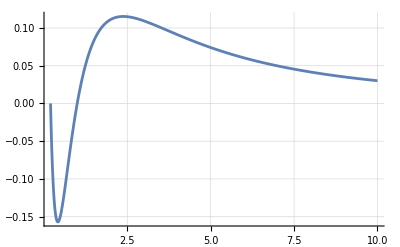

```mathematica
Plot[Subscript[f, 1,2,3]'[x],{x,0.2,10},PlotRange->All,GridLines->Automatic]
```

### Using Pure Functions

An alternative way of writing functions is to use pure functions.

My preference is to introduce functions and pure functions using the map notation:

Mathematics | Wolfram Language
f(x)=x^2 | f[x_]:=x^2
f:x↦x^2 | Piecewise[{{#^2&, Pure function}, {f=x↦x^2, As a map}}]

When you solve a differential equation for a function, the solution is returned as list of lists of replacement rules (because there can be multiple solutions)

Use DSolve to solve y'(x)==y(x):

```mathematica
dsol=DSolve[y'[x]==y[x]]
```

{{y(x)→1 ⅇ^x}}

This is a literal rule for y(x).

Substituting the solution back into the differential equation, only the function, not its derivative, gets evaluated:

```mathematica
y'[x]==y[x]/.dsol
```

{y'(x)==1 ⅇ^x}

When you solve a differential equation for a pure function the solution is returned as list of lists of replacement rules as pure functions.

Solve y'(x)==y(x) for y:

```mathematica
dsol=DSolve[y'[x]==y[x],y,x]
```

{{y→({x}↦1 ⅇ^x)}}

Check that the differential equation is satisfied:

```mathematica
y'[x]==y[x]/.First[dsol]
```

True

### Application: Newton’s Method

Newton's method or Newton-Raphson iteration is an a iterative root-finding algorithm which computes the roots (or zeroes) of a function, f(z), as the fixed-point of the Newton iteration, z↦z-(f(z))/(f'(z)).

The built-in FindRoot function automatically uses Newton's Methodpaclet:tutorial/UnconstrainedOptimizationMethodsForLocalMinimization#440876683 and computes the symbolic derivative automatically if the function is explicitly differentiable.

Use FindRoot to compute the root of x^4-3 near x=1 with a WorkingPrecision of 20:

```mathematica
FindRoot[x^4-3,{x,1},WorkingPrecision->20]
```

{x→1.3160740129524924608}

Check this answer:

```mathematica
x^4-3/.%
```

0.

Alternatively, implement Newton’s method for general f(z) with initial guess x_0, default tolerance, ϵ=10^-10, and default number of interations, n=15, using pure functions and FixedPoint:

```mathematica
NewtonsMethod[f_Function,x0_,ε_:10^-10,n_:15]:=
FixedPoint[x↦x-f[x]/f'[x],x0,n,SameTest->({u,v}↦Abs[u-v]<ε)]
```

This implementation using FixedPoint is simple and direct. The derivative is computed automatically and there is no need to combine looping constructs with a break statement—as is the case in most other languages.

Compue the root of x↦x^4-3 near x=1 (entered using ` as a number of Precision 20):

```mathematica
NewtonsMethod[x↦x^4-3,1`20]
```

1.3160740129524925

Check that this result is consistent with the default tolerance:

```mathematica
%^4-3
```

0.

Use Newton's method to compute the n-th roots of unity, i.e., the roots of f(z)=z^n-1.

Compute the Newton iteration, z→z-(f(z))/(f'(z)) for f(z)=z^n-1:

```mathematica
z-(f(z))/(f'(z))/.f->(z↦z^n-1)//Simplify
```

(z (z^-n+n-1))/n

Implement Newton’s method for finding the n^th roots of unity f(z)=z^n-1  as a compiled function of n∈ℤ and z∈ℂ by applying Compile to the Arg—to show to which root the iteration converges—of the FixedPoint, with a maximum of 50 interations:

```mathematica
RootsOfUnity=Compile[{{n,_Integer},{c,_Complex}},Arg[FixedPoint[z↦(z (z^-n+n-1))/n,c,50]]];
```

Use DensityPlot to display the convergence of Newton’s method when computing the 5^th roots of unity:

```mathematica
DensityPlot[RootsOfUnity[5,x+ⅈ y],{x,y}∈Disk[{0,0},1.2],PlotPoints->300,ColorFunction->Hue,ImageSize->Large]
```

-Graphics-

Tech Notes

Code using the map notation is reasier to read and corresponds to standard mathematical notation, e.g {x,y}↦x^2+y^2.

Multiple nested # and &’s in an expression usually need extra parentheses to avoid conflicts between uses of # in different functions.

Numbered options are used in many functions, e.g., #5 in the MeshFunctions for ParametricPlot3D, which many users find confusing.

A related syntactical issue is the use of “nested heads”. In general, separating “parameters” from “variables”, using f[n][x] instead of f[n,x] is preferable.

Vocabulary

Plotpaclet:ref/Plot[f,{x,x_min,x_max}] |   | generates a plot of f as a function of x from x_min to x_max
FindRootpaclet:ref/FindRoot[f,{x,x_0}]  |   | searches for a numerical root of f, starting from the point x=x_0
DSolvepaclet:ref/DSolve[eqn] |   | solves a differential equation eqn
FixedPointpaclet:ref/FixedPoint[f,expr] |   | starts with expr, then applies f repeatedly until the result no longer changes.
SameTest |   | an option whose setting gives a pairwise comparison function to determine whether expressions should be considered the same
Precision |   | numbers entered in the form digits`p are taken to have precision p
Compilepaclet:ref/Compile[{x_1,x_2,…},expr] |   | creates a compiled function that evaluates expr assuming
numerical values of the x_i
Argpaclet:ref/Arg[z] |   | gives the argument of the complex number z
DensityPlotpaclet:ref/DensityPlot[f,{x,y}∈reg] |   | takes the variables {x,y} to be in the geometric region reg